```mathematica
ccColor=RGBColor["#ff1f5b"];
```

```mathematica
ctColor=Blue;
```

```mathematica
(*********************************)
```

```mathematica
dateMouseSessionListV1CC={{"051623","Mouse23112","Session1"},{"051723","Mouse23112","Session1"},{"051623","Mouse23166","Session1"},{"051723","Mouse23166","Session1"},{"043023","Mouse23184","Session1"},{"050123","Mouse23184","Session1"},{"050423","Mouse23184","Session1"},{"052523","Mouse23158","Session1"},{"052923","Mouse23158","Session1"}};
```

```mathematica
dateMouseSessionListV1CT={{"041823","Mouse21531","Session1"},{"041923","Mouse21531","Session1"},{"041823","Mouse23138","Session1"},{"041923","Mouse23138","Session1"},{"042023","Mouse23138","Session1"},{"050523","Mouse23195","Session1"},{"051723","Mouse21532","Session1"},{"051823","Mouse21532","Session1"},{"052523","Mouse23195","Session1"}};
```

```mathematica
(**********************************************)
(*******Generate plots in Figure S4L****************) 
(**********************************************)
```

```mathematica
meanDFFpupilCCV1CC=ToExpression/@Import["C:/Users/garrett/Desktop/PopulationAnalyses/Observational/Dendrites/V1CC/ValuesForPlotting/meanDFFpupilCrossCorr_V1CC_nonDupROIs.txt","List"];
```

```mathematica
semDFFpupilCCV1CC=ToExpression/@Import["C:/Users/garrett/Desktop/PopulationAnalyses/Observational/Dendrites/V1CC/ValuesForPlotting/semDFFpupilCrossCorr_V1CC_nonDupROIs.txt","List"];
```

```mathematica
(*********)
```

```mathematica
meanDFFpupilCCV1CT=ToExpression/@Import["C:/Users/garrett/Desktop/PopulationAnalyses/Observational/Dendrites/V1CT/ValuesForPlotting/meanDFFpupilCrossCorr_V1CT_nonDupROIs.txt","List"];
```

```mathematica
semDFFpupilCCV1CT=ToExpression/@Import["C:/Users/garrett/Desktop/PopulationAnalyses/Observational/Dendrites/V1CT/ValuesForPlotting/semDFFpupilCrossCorr_V1CT_nonDupROIs.txt","List"];
```

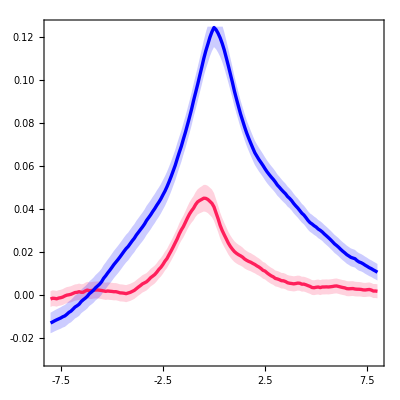

```mathematica
ListLinePlot[{Part[#,2]&/@meanDFFpupilCCV1CC,Part[#,2]&/@meanDFFpupilCCV1CC+(Part[#,2]&/@semDFFpupilCCV1CC),Part[#,2]&/@meanDFFpupilCCV1CC-(Part[#,2]&/@semDFFpupilCCV1CC),Part[#,2]&/@meanDFFpupilCCV1CT,Part[#,2]&/@meanDFFpupilCCV1CT+(Part[#,2]&/@semDFFpupilCCV1CT),Part[#,2]&/@meanDFFpupilCCV1CT-(Part[#,2]&/@semDFFpupilCCV1CT)},Filling->{1->{{2},Directive[Opacity[0.2],ccColor]},1->{{3},Directive[Opacity[0.2],ccColor]},4->{{5},Directive[Opacity[0.2],ctColor]},4->{{6},Directive[Opacity[0.2],ctColor]}},PlotStyle->{{ccColor,Thickness[0.006]},Transparent,Transparent,{ctColor,Thickness[0.006]},Transparent,Transparent},DataRange->{-8,8},PlotRange->{{-8,8},{-0.03,0.125}},FrameTicks->{{LinTicks[-0.03,0.125,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-8,8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
(**********************************************)
(*******Generate plots in Figure S4M****************) 
(**********************************************)
```

```mathematica
meanDFFpupilPhaseV1CC=ToExpression/@Import["C:/Users/garrett/Desktop/PopulationAnalyses/Observational/Dendrites/V1CC/ValuesForPlotting/meanDFFpupilPhase_V1CC_nonDupROIs.txt","List"];
```

```mathematica
semDFFpupilPhaseV1CC=ToExpression/@Import["C:/Users/garrett/Desktop/PopulationAnalyses/Observational/Dendrites/V1CC/ValuesForPlotting/semDFFpupilPhase_V1CC_nonDupROIs.txt","List"];
```

```mathematica
meanDFFpupilPhaseV1CT=ToExpression/@Import["C:/Users/garrett/Desktop/PopulationAnalyses/Observational/Dendrites/V1CT/ValuesForPlotting/meanDFFpupilPhase_V1CT_nonDupROIs.txt","List"];
```

```mathematica
semDFFpupilPhaseV1CT=ToExpression/@Import["C:/Users/garrett/Desktop/PopulationAnalyses/Observational/Dendrites/V1CT/ValuesForPlotting/semDFFpupilPhase_V1CT_nonDupROIs.txt","List"];
```

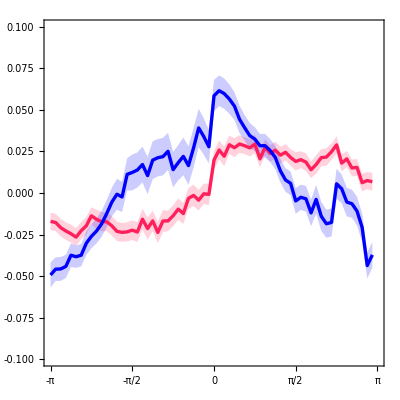

```mathematica
ListLinePlot[{Part[#,2]&/@meanDFFpupilPhaseV1CC,Part[#,2]&/@meanDFFpupilPhaseV1CC+(Part[#,2]&/@semDFFpupilPhaseV1CC),Part[#,2]&/@meanDFFpupilPhaseV1CC-(Part[#,2]&/@semDFFpupilPhaseV1CC),Part[#,2]&/@meanDFFpupilPhaseV1CT,Part[#,2]&/@meanDFFpupilPhaseV1CT+(Part[#,2]&/@semDFFpupilPhaseV1CT),Part[#,2]&/@meanDFFpupilPhaseV1CT-(Part[#,2]&/@semDFFpupilPhaseV1CT)},Filling->{1->{{2},Directive[Opacity[0.2],ccColor]},1->{{3},Directive[Opacity[0.2],ccColor]},4->{{5},Directive[Opacity[0.2],ctColor]},4->{{6},Directive[Opacity[0.2],ctColor]}},PlotStyle->{{ccColor,Thickness[0.006]},Transparent,Transparent,{ctColor,Thickness[0.006]},Transparent,Transparent},DataRange->{-π,(31 π)/32},PlotRange->{{-π,π},{-0.1,0.1}},FrameTicks->{{LinTicks[-0.1,0.1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-π,π,π/2,4,TickLabelFunction->(Rationalize[#/π]*π&),MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
(**********************************************)
(*******Generate plots in Figure S4N****************) 
(**********************************************)
```

```mathematica
peakCCValsV1CC=ToExpression/@Import["C:/Users/garrett/Desktop/PopulationAnalyses/Observational/Dendrites/V1CC/ValuesForPlotting/peakDFFpupilCC_V1CC.txt","List"];
```

```mathematica
peakCCValsV1CT=ToExpression/@Import["C:/Users/garrett/Desktop/PopulationAnalyses/Observational/Dendrites/V1CT/ValuesForPlotting/peakDFFpupilCC_V1CT.txt","List"];
```

```mathematica
(**********************)
```

```mathematica
ccAxonCharts=Show[BoxWhiskerChart[peakCCValsV1CC,{{"Whiskers", Directive[Darker@ccColor,Thick]}, {"Fences", Directive[Darker@ccColor,Thick]},{"MedianMarker", Directive[Darker@ccColor,Thickness[0.009]]}},PlotRange->{All,{-0.07,0.5}},ChartStyle->Directive[ccColor,Opacity[0.3]],Frame->False],DistributionChart[peakCCValsV1CC,PlotRange->{All,{-0.07,0.5}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],ccColor],Frame->False],FrameTicks->{{LinTicks[-0.07,0.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
ctAxonCharts=Show[BoxWhiskerChart[peakCCValsV1CT,{{"Whiskers", Directive[Darker@ctColor,Thick]}, {"Fences", Directive[Darker@ctColor,Thick]},{"MedianMarker", Directive[Darker@ctColor,Thickness[0.009]]}},PlotRange->{All,{-0.07,0.5}},ChartStyle->Directive[ctColor,Opacity[0.3]],Frame->False],DistributionChart[peakCCValsV1CT,PlotRange->{All,{-0.07,0.5}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],ctColor],Frame->False],FrameTicks->{{LinTicks[-0.07,0.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[peakCCValsV1CT,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{-0.07,0.5}},ChartStyle->Transparent,Frame->False],DistributionChart[peakCCValsV1CT,PlotRange->{All,{-0.07,0.5}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[-0.07,0.5,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

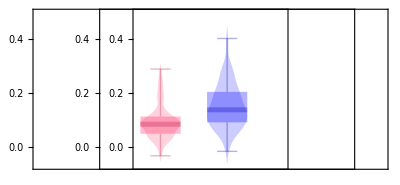

```mathematica
GraphicsRow[{ccAxonCharts,ctAxonCharts,transp},Spacings->{{-280,-280,-320}}]
```